Lab 10: Neutron Detectors

J.R. Powers-Luhn
NE550 Thursday 17:30

Utility tools

Raw SPE data

```mathematica
speraw[filename_,directory_]:=Import[directory<>filename]
```

SPE Data length

```mathematica
spedatalength[filename_,directory_]:=ToExpression[StringSplit[Import[directory<>filename][[12]]][[1,2]]]
```

```mathematica
spedatalength["He3 60s 0.5microseconds.Spe",NotebookDirectory[]<>"data/neutron detectors/"]
```

1023

SPE File Importer

```mathematica
spedata[filename_,directory_]:=ToExpression[Import[directory<>filename][[13;;13+spedatalength[filename,directory]]]][[;;,1]]
```

Time of count in SPE file

```mathematica
spetime[filename_,directory_]:=ToExpression[StringSplit[Import[directory<>filename][[10]]][[1,1]]]
```

^3 He neutron detector

1. Properly plot the ^3 He spectra for each shaping time investigated. Put all traces on a single pot, and use the full energy peak that shows up in at least some of the spectra to convert the abscissa to energy (Q-value is 764 keV).

```mathematica
shapingTimes={0.5,1,2,3,6,10}
filenameList=Table["He3 60s "<>ToString[i]<>"microseconds.Spe",{i,shapingTimes}]
```

{0.5,1,2,3,6,10}

{He3 60s 0.5microseconds.Spe,He3 60s 1microseconds.Spe,He3 60s 2microseconds.Spe,He3 60s 3microseconds.Spe,He3 60s 6microseconds.Spe,He3 60s 10microseconds.Spe}

```mathematica
directory=NotebookDirectory[]<>"data/neutron detectors/";
```

```mathematica
qvalue=762(*keV*);
```

```mathematica
peakindexes={68, 80, 88, 90, 94, 96}; (* From attached python script *)
xfrmfacts = qvalue / peakindexes //N
```

{11.2059,9.525,8.65909,8.46667,8.10638,7.9375}

```mathematica
xrange=Range[1,1023];
```

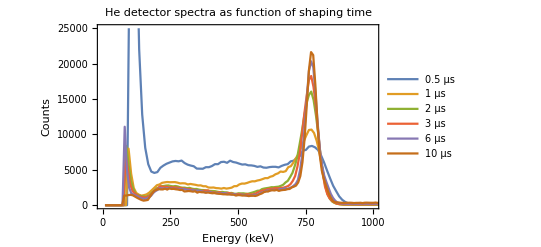

```mathematica
ListPlot[Table[Multicolumn[Join[xrange*xfrmfacts[[i]],spedata[filenameList[[i]],directory]],2]//First,{i,Length[filenameList]}],PlotRange->{{0,1000},{0,25000}},PlotLabel->Style["He detector spectra as function of shaping time",24,Black],ImageSize->Full,Joined->True,PlotLegends->Placed[Table[ToString[i]<>" μs",{i,shapingTimes}],{0.5,0.75}],Frame->True,FrameLabel->{Style["Energy (keV)",Black,20],Style["Counts",Black,20]},FrameTicksStyle->Directive[Black,16]]
```

2. From the plot, and in a text-style cell, discuss what shaping time is needed to obtain a quality spectrum from the ^3 He detector (i.e., full energy peak with wall effects).

In order to get a quality spectrum, a shaping time of 2μs is necessary, though for this source a longer shaping time is appropriate.

3. In another text-style cell, comment on the reason behind the required shaping time. That is, why is the peaking time found necessary required? What is it a function of?

4. If we wish to only count neutron events, identify which energy value on the abscissa would be chosen to discriminate counts from the very low energy region of the spectrum. Put your answer in a text-style cell.

BF_3 neutron detector

1. Properly plot the BF_3 spectra for each shaping time investigated. Put all traces on a single plot, and use the full energy peak that shows up in at least some of the spectra to convert the abscissa to energy (Q-value is 2.79 MeV, but the ^7 Li product only goes to the ground state 6% of the time.

```mathematica
shapingTimes={0.5,1,2,3,6,10}
filenameList=Table["BF3 120s "<>ToString[i]<>"microseconds.Spe",{i,shapingTimes}]
```

{0.5,1,2,3,6,10}

{BF3 120s 0.5microseconds.Spe,BF3 120s 1microseconds.Spe,BF3 120s 2microseconds.Spe,BF3 120s 3microseconds.Spe,BF3 120s 6microseconds.Spe,BF3 120s 10microseconds.Spe}

```mathematica
directory=NotebookDirectory[]<>"data/neutron detectors/";
```

```mathematica
qvalue=2790(*keV*);
```

```mathematica
peakindexes={133,150,164,167,174,181};

xfrmfacts = qvalue / peakindexes //N
```

{20.9774,18.6,17.0122,16.7066,16.0345,15.4144}

```mathematica
xrange=Range[1,1023];
```

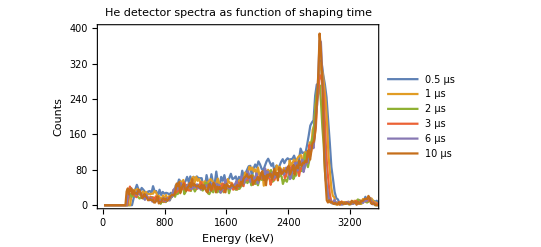

```mathematica
ListPlot[Table[Multicolumn[Join[xrange*xfrmfacts[[i]],spedata[filenameList[[i]],directory]],2]//First,{i,Length[filenameList]}],PlotRange->{{0,3500},{0,400}},PlotLabel->Style["He detector spectra as function of shaping time",24,Black],ImageSize->Full,Joined->True,PlotLegends->Placed[Table[ToString[i]<>" μs",{i,shapingTimes}],{0.5,0.75}],Frame->True,FrameLabel->{Style["Energy (keV)",Black,20],Style["Counts",Black,20]},FrameTicksStyle->Directive[Black,16]]
```

2. From the plot, and in a text-style cell, discuss what shaping time is needed to obtain a quality spectrum from the BF_3 detector (i.e., full energy peak with wall effects).

For this detector and source, a short shaping time of 0.5μs is appropriate. The incoming neutrons are able to deposit most of their energy in this time range, meaning that spectroscopy is possible based on this relatively distinct peak.

3. In another text-style cell, comment on the reason behind the required shaping time. That is, why is the peaking time found necessary required? What is it a function of?

4. If we wish to only count neutron events, identify which energy value on the abscissa would be chosen to discriminate counts from the very low energy region of the spectrum. Put your answer in a text-style cell.

Boron loaded organic scintillator

1. Plot the two spectra on the sample plot (properly formatted) when the Na-22 source is and is not present near the boron loaded organic scintillator.

```mathematica
directory=NotebookDirectory[]<>"data/boron loaded organic scintillator/";
filenameList={"with Na.Spe","without Na.Spe"};
```

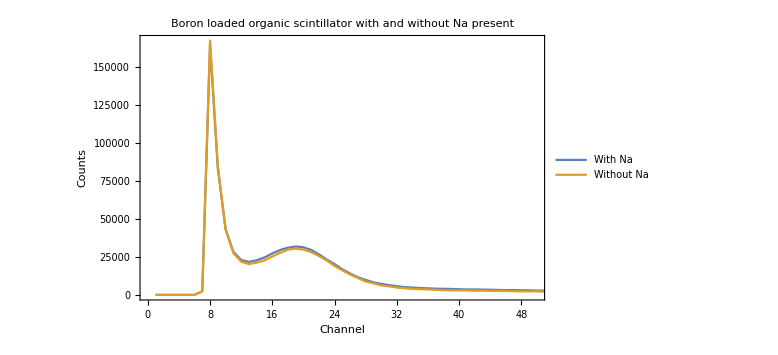

```mathematica
ListPlot[Table[spedata[i,directory],{i,filenameList}],PlotRange->{{0,50},All},Joined->True,ImageSize->Large,PlotLegends->Placed[{"With Na","Without Na"},{0.85,0.85}],Frame->True,FrameLabel->{Style["Channel",Black,20],Style["Counts",Black,20]},PlotLabel->Style["Boron loaded organic scintillator\n with and without Na present",24,Black],FrameTicksStyle->Directive[Black,16]]
```

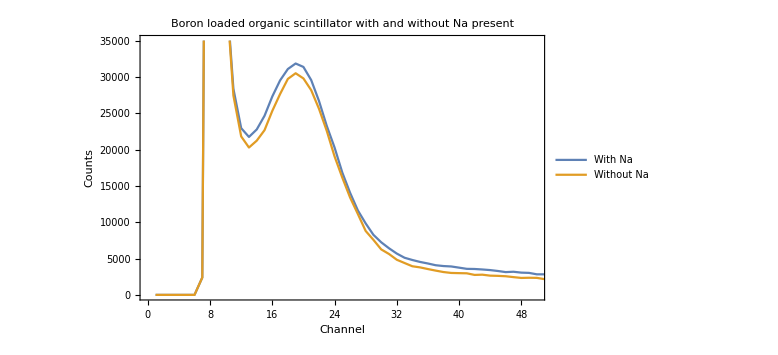

```mathematica
ListPlot[Table[spedata[i,directory],{i,filenameList}],PlotRange->{{0,50},{0,35000}},Joined->True,ImageSize->Large,PlotLegends->Placed[{"With Na","Without Na"},{0.85,0.85}],Frame->True,FrameLabel->{Style["Channel",Black,20],Style["Counts",Black,20]},PlotLabel->Style["Boron loaded organic scintillator\n with and without Na present",24,Black],FrameTicksStyle->Directive[Black,16]]
```

2. Using the drawing tools, identify the thermal neutron response in both spectra (again, this is the plot in (1)) and the Na-22 contribution observed in one of the two spectra.

3. In a text-style cell, comment on whether the Na-22 source interferes with counting thermal neutrons with this organic scintillator. Specifically comment on the threshold (i.e., value on the abscissa) you would choose to discriminate between gamma-rays and neutrons.

EJ-299 Pulse Shape Discrimination Plastic

1. Plot the two spectra on the sample plot (properly formatted) when the Na-22 source is and is not present near the EJ-299 detector.

2. Using the drawing tools, identify the fast neutron response in both spectra (again, this is the plot in (1)) and the Na-22 contribution observed in one of the two spectra.

3. In a text-style cell, comment on whether the Na-22 source interferes with counting fast neutrons with this organic scintillator. Specifically comment on the threshold (i.e., value on the abscissa) you would choose to discriminate between gamma-rays and neutrons, if any is appropriate at all.

4. Import the 2D PSD plot collected using the V1720 digitizer with PSD capability. Looking at this plot, qualitatively discuss, in a text-style cell, how well EJ-299 discriminates signals from gamma rays and neutrons. Pay particular attention to the lower integrated pulse region (low end of abscissa). For the abscissa value where a clear separation is observed between gamma rays and neutrons, theorize if this abscissa value is superior to just collecting a pulse height spectrum and choosing some threshold, if any (plot from (1) and discussion in (3)).